```mathematica
2-2
```

0

# Iteration Techniques

Nicholas Wheeler
23 November 2011

### Introduction

In my recent "Experimental Mathematical Physics" seminar (9 November 2011) I had occasion to remark (Slide 30: §5. Opened Doors) that my method for executing site-specific random walks on DC circuits seemed to place me in position to finally complete my Reed College thesis ("The classical mechanics of non-classical systems," 1955), which contemplated "random walks on phase space with mean positions that satisfy Hamilton's canonical equations." I was motivated to exlore that possibility when I was visited in my office by Sina Zeytinoglu, who is writing a thesis with Darrell Schroeter and had been inspired by aspects of my seminar to ask whether I might have something to say about random walks on "corrugated graphine." 

I begin with remarks intended to cultivate some relevant technique.

### Numerical and iterative solution of simple diffrerential equations

The query

```mathematica
?NDSolve
```

NDSolve[eqns,y,{x,x_min,x_max}] finds a numerical solution to the ordinary differential equations eqns for the function y with the independent variable x in the range x_min to x_max. 
NDSolve[eqns,y,{x,x_min,x_max},{t,t_min,t_max}] finds a numerical solution to the partial differential equations eqns. 
NDSolve[eqns,{y_1,y_2,…},{x,x_min,x_max}] finds numerical solutions for the functions y_i.

supplies (among others) this instructive instance of relevant commands:

```mathematica
s=NDSolve[{x'[t]==-y[t]-x[t]^2,y'[t]==2x[t]-y[t]^3,x[0]==y[0]==1},{x,y},{t,20}]
```

{{x→InterpolatingFunction[{{0.,20.}},<>],y→InterpolatingFunction[{{0.,20.}},<>]}}

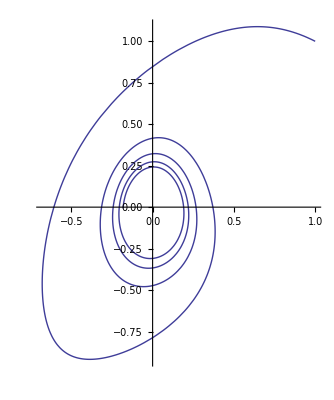

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,20}]
```

I assume Mathematica proceeds by some optimized iterative routine. Here is an even simpler example, borrowed from the classical theory of harmonic oscillators:

```mathematica
H[x_,p_]:=1/2 x^2+1/2 3 p^2
```

```mathematica
D[H[x,p], p]
-D[H[x,p], x]
```

3 p

-x

```mathematica
OscillatorOrbit=NDSolve[{x'[t]==3p[t],p'[t]==-x[t],x[0]==0,p[0]==1},{x,p},{t,0,10}]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],p→InterpolatingFunction[{{0.,10.}},<>]}}

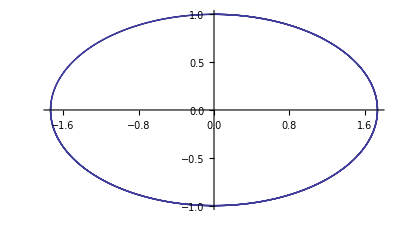

```mathematica
ParametricPlot[Evaluate[{x[t],p[t]}/.OscillatorOrbit],{t,0,10}]
```

Here I illustrate an unsophisticated procedure intended to accomplish the same calculation:

```mathematica
f[z_]:={z⟦1⟧+τ 3z⟦2⟧,z⟦2⟧-τ z⟦1⟧}
```

```mathematica
τ=.01;
x=0;
y=1;
```

```mathematica
SuccessivePoints=Simplify[NestList[f,{x,y},10000]];
```

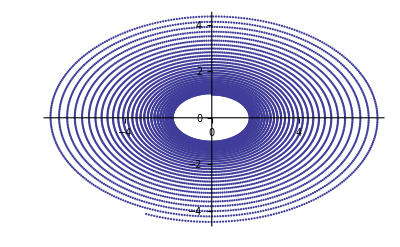

```mathematica
ListPlot[SuccessivePoints,AxesOrigin->{0,0},PlotStyle->PointSize[0.004]]
```

To test whether the failure of the curve to close on itself can be attributed to the size of τ I repeat the calculation with an assortment of alternative τ-values:

```mathematica
τ=0.001;
```

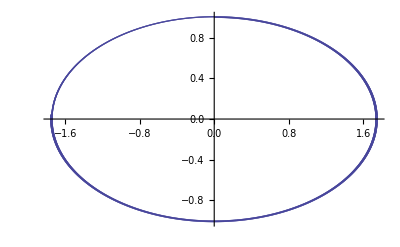

```mathematica
SuccessivePoints=Simplify[NestList[f,{x,y},10000]];

ListPlot[SuccessivePoints,AxesOrigin->{0,0},PlotStyle->PointSize[0.001]]
```

and reduce it again by yet another factor of 10:

```mathematica
τ=0.0001;
```

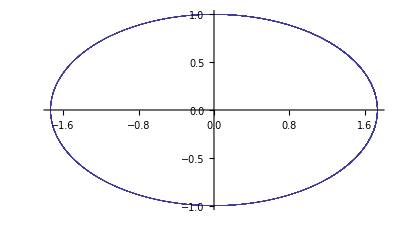

```mathematica
SuccessivePoints=Simplify[NestList[f,{x,y},50000]];

ListPlot[SuccessivePoints,AxesOrigin->{0,0},PlotStyle->PointSize[0.001],AspectRatio->Automatic]
```

It is amazing (but gratifying!) that Mathematica is—though the computational burden has been much increased—still able to complete its work in only a few seconds.

Here I repeat the calculation with a relatively large τ-value:

```mathematica
τ=.1;
```

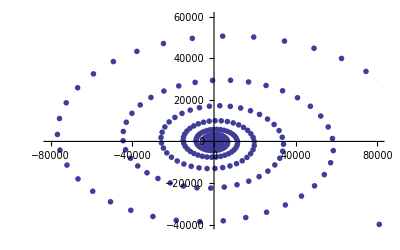

```mathematica
SuccessivePoints=Simplify[NestList[f,{x,y},800]];

ListPlot[SuccessivePoints,AxesOrigin->{0,0},PlotStyle->PointSize[0.01],AspectRatio->Automatic,PlotRange->{{-80000,80000},{-40000,60000}}]
```

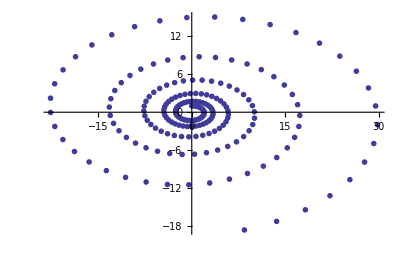

```mathematica
SuccessivePoints=Simplify[NestList[f,{x,y},200]];

ListPlot[SuccessivePoints,AxesOrigin->{0,0},PlotStyle->PointSize[0.01],AspectRatio->Automatic]
```

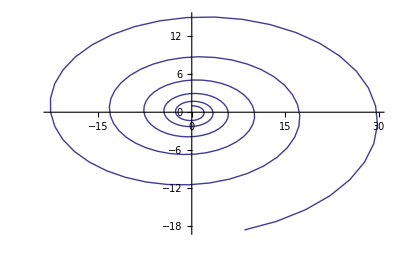

```mathematica
SuccessivePoints=Simplify[NestList[f,{x,y},200]];

ListLinePlot[SuccessivePoints,AxesOrigin->{0,0},PlotStyle->PointSize[0.01],AspectRatio->Automatic]
```

### Stochastic classical motion

This subject—pioneered by Einstein, Smoluchowski, Langevin, Fokker, Planck…and deepened by Ito, Kolmogorov,  Bogoliubov…—has given rise to an enormous literature, with most of which I am at present totally ignorant: see

```mathematica
Hyperlink["Stochastic DEs","http://en.wikipedia.org/wiki/Stochastic_differential_equation"]
```

```mathematica
Hyperlink["Fokker-Planck","http://en.wikipedia.org/wiki/Fokker-Planck_equation"]
```

for basic information, links and references. Google also notes the existence of sites having to do specifically with the application of Mathematica to problems of this general nature.

Here I will be stumbling along, clumsily reinventing the wheel, with a very limited objective.

One can think of a variety of ways to introduce stochastic elements into classical (also quantum?) equations of motion.  I begin with exporation of an idea which is conspicuously devoid of direct physical motivation, which has only a sentimental circumstance to recomment it: it is the idea that I attempted to address in my undergraduate thesis.

#### Classical lattice dynamics

A particle moves on the phase plane under general control of a Hamiltonian H[x, p] not contiuously but in a series of hops (time measured in discrete intervals of duration τ), subject to this constraint: every hop is—with equal probability—parallel either to the x-axis or the p-axis.

```mathematica
?RandomChoice
```

RowBox[{"RandomChoice", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] gives a pseudorandom choice of one of the SubscriptBox[StyleBox["e", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"RandomChoice", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"]}], "]"}] gives a list of StyleBox["n", "TI"] pseudorandom choices. 
RowBox[{"RandomChoice", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] gives an RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], "×", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], "×", "…", " "}] array of pseudorandom choices. 
RowBox[{"RandomChoice", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["w", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["w", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "->", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] gives a pseudorandom choice weighted by the SubscriptBox[StyleBox["w", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"RandomChoice", "[", RowBox[{RowBox[{StyleBox["wlist", "TI"], "->", StyleBox["elist", "TI"]}], ",", StyleBox["n", "TI"]}], "]"}] gives a list of StyleBox["n", "TI"] weighted choices.
RowBox[{"RandomChoice", "[", RowBox[{RowBox[{StyleBox["wlist", "TI"], "->", StyleBox["elist", "TI"]}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] gives an RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], "×", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], "×", StyleBox["…", "TR"]}] array of weighted choices.

```mathematica
RandomChoice[{0,1},100]
```

{1,1,0,0,0,1,0,0,0,1,0,1,0,0,1,0,1,1,1,0,0,0,0,1,1,1,1,0,1,1,1,1,0,1,1,0,0,0,0,0,1,1,0,0,1,0,0,0,1,1,1,0,0,1,0,1,0,0,1,0,1,1,1,1,0,1,1,1,0,0,0,0,0,1,1,0,0,1,0,0,1,0,1,0,1,1,0,1,1,1,0,1,0,0,0,1,1,0,0,1}

```mathematica
Tally[%]
```

{{1,49},{0,51}}

```mathematica
f[z_]:=RandomChoice[{{z⟦1⟧+τ 3z⟦2⟧,z⟦2⟧},{z⟦1⟧,z⟦2⟧-τ z⟦1⟧}}]
```

```mathematica
τ=.01;
x=0;
p=1;
```

```mathematica
SuccessivePoints=Simplify[NestList[f,{x,p},1000]];
```

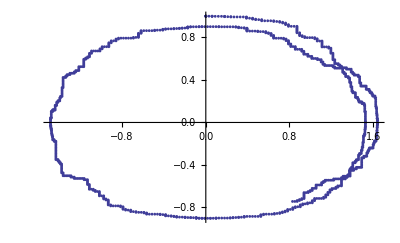

```mathematica
ListPlot[SuccessivePoints,AxesOrigin->{0,0},PlotStyle->PointSize[0.005],AspectRatio->Automatic]
```

```mathematica
τ=.002;
x=0;
p=1;
```

```mathematica
SuccessivePoints=Simplify[NestList[f,{x,p},15000]];
```

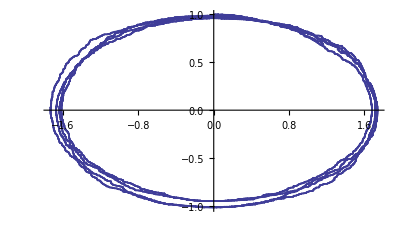

```mathematica
RandomizedOrbit=ListPlot[SuccessivePoints,AxesOrigin->{0,0},PlotStyle->PointSize[0.003],AspectRatio->Automatic]
```

```mathematica
Clear[x,p,t]
```

```mathematica
OscillatorOrbit=NDSolve[{x'[t]==3p[t],p'[t]==-x[t],x[0]==0,p[0]==1},{x,p},{t,0,10}]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],p→InterpolatingFunction[{{0.,10.}},<>]}}

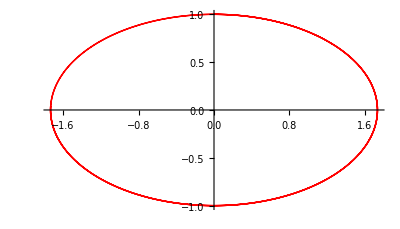

```mathematica
NonrandomOrbit=ParametricPlot[Evaluate[{x[t],p[t]}/.OscillatorOrbit],{t,0,10},PlotStyle->{Thick,Red}]
```

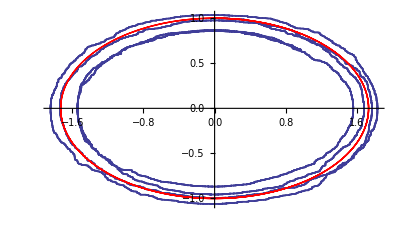

```mathematica
Show[{RandomizedOrbit,NonrandomOrbit}]
```

We are in position to study motion of the mean, but that would involve heavy Monte Carlo work that I am not motivated to undertake. One could introduce a "more physical" mechanism for introducing randomness…as is presumably contemplated in serious stochastic DE work…but again my motivation fails me. 

Note the clear violation of energy conservation, which I suppose is to be expected if randomness is considered to be a result of uncontrolled perturbative interaction with an "environment." Energy non-conservation would be expected even if that interaction were "more physical."

If my undergraduate self were to sketch his idea to me today I would advise him to forget it, for it seems incapable of capturing any of the essentials of quantum mechanics. A worthy objective would be to demonstrate a mechanism whereby the classical distribution

P[x,p,t]=δ[x-x[t]]δ[p-p[t]]

acquires features of the Wigner distribution, of which the most essential is

∫P[x,p]ⅆxⅆp=1

But that looks pretty hopeless to me at the moment (maybe in another 56 years?).

Possibly more workable/interesting is this idea: Introduce a random jiggle into

```mathematica
Subscript[ψ, t]=𝕌[t] Subscript[ψ, 0]
```

### Motion in a "periodic Sina Zeytinoglu potential"

We are led by my understanding of the picture Zeytinoglu has in mind to contemplate a dynamic random walk on the 2D plane (4D phase space), in the presence of a spatially periodic potential. I construct a couple of such potentials:

#### Illustrative spatially periodic potentials in 2D

A.  Sinusoidal Corregations

```mathematica
Clear[x,y,p,q,t]
```

```mathematica
V[x_,y_]:=1+Sin[2π x]
```

```mathematica
Plot3D[1+Sin[2π x],{x,0,4},{y,0,4}, AxesLabel->{"x","y","V"}]
```

-Graphics3D-

The Hamilton is of the form

```mathematica
H[p,q,x,y]=Subscript[H, 1][p,x]+Subscript[H, 2][q,y]=(1/2)[p^2+q^2]+1+Sin[2π x]
```

so the equations of motion separate:

```mathematica
x'[t]==p[t]
p'[t]==-2π Cos[2π x[t]]

y'[t]==q[t]
q'[t]==0
```

The {y, q} motion is unaccelerated uniform:

```mathematica
y[t]==Subscript[y, 0]+Subscript[q, 0] t
q[t]==Subscript[q, 0]
```

The {x. p} motion is pendular—oscillatory if E < 2 and libational if E > 2:

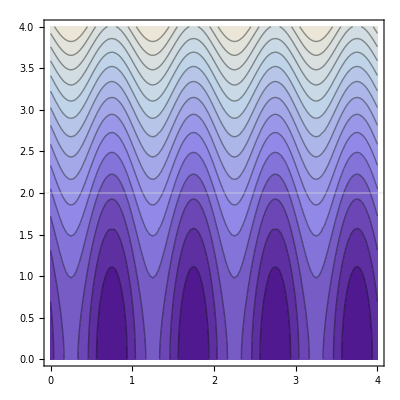

```mathematica
EnergyContours=ContourPlot[1/2 p^2+1+Sin[2π x],{x,0,4},{p,0,4},Contours->15,GridLines->{{},{2}}]
```

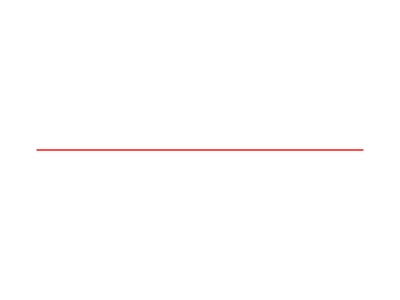

```mathematica
CriticalMomentum=Graphics[{Red,Thick,Line[{{0,2},{4,2}}]}]
```

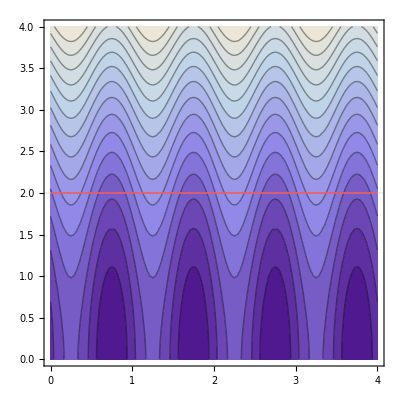

```mathematica
Show[{EnergyContours,CriticalMomentum}]
```

```mathematica
?DSolve
```

DSolve[eqn,y,x] solves a differential equation for the function y, with independent variable x. 
DSolve[{eqn_1,eqn_2,…},{y_1,y_2,…},x] solves a list of differential equations. 
DSolve[eqn,y,{x_1,x_2,…}] solves a partial differential equation.

```mathematica
DSolve[{x'[t]==p[t],p'[t]==-2π Cos[2π x[t]]},{x,p},t]
```

{{p→Function[{t},√2 √(C[1]-Sin[1/2 (π-4 JacobiAmplitude[π (-√2 t √(-1+C[1])-√(-1+C[1]) C[2]),-2/(-1+C[1])])])],x→Function[{t},(π-4 JacobiAmplitude[π (-√2 t √(-1+C[1])-√(-1+C[1]) C[2]),-2/(-1+C[1])])/(4 π)]},{p→Function[{t},-√2 √(C[1]-Sin[1/2 (π-4 JacobiAmplitude[π (√2 t √(-1+C[1])-√(-1+C[1]) C[2]),-2/(-1+C[1])])])],x→Function[{t},(π-4 JacobiAmplitude[π (√2 t √(-1+C[1])-√(-1+C[1]) C[2]),-2/(-1+C[1])])/(4 π)]}}

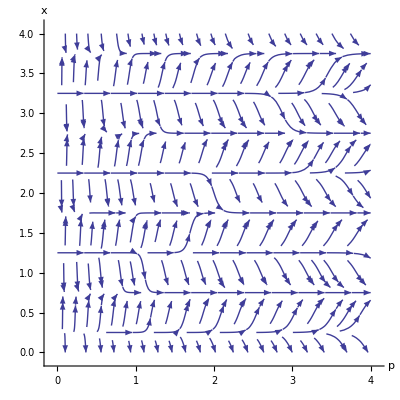

```mathematica
StreamPlot[{p,-2π Cos[2π x]},{p,0,4},{x,0,4},Frame->False,Axes->True,AxesLabel->{"p","x"}]
```

```mathematica
Clear[x]
```

```mathematica
PDF[BetaDistribution[α,β],x]
```

((1-x)^(-1+β) x^(-1+α))/Beta[α,β]

```mathematica
Manipulate[Plot[.5((1-x)^(-1+β) x^(-1+α))/Beta[α,β],{x,0,1}],{α,0,5},{β,0,5}]
```